# DST

10 π

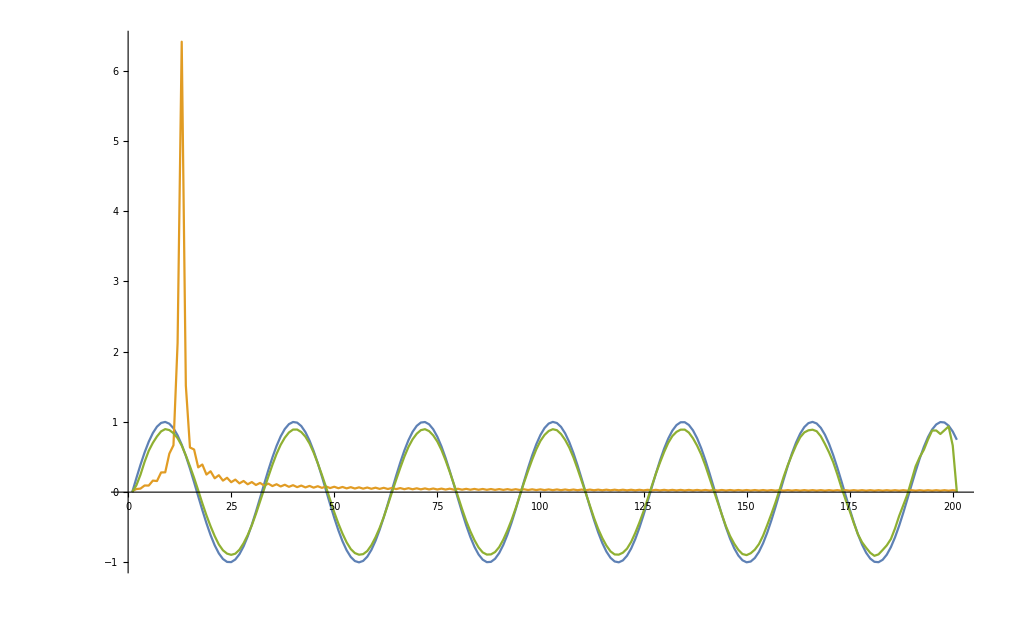

```mathematica
Clear[t,x,f,n,m]
n=200;
f=Sin[#/5]&;
fp=FunctionPeriod[f[x],x]
nHalf=Round[n/2];
F[p_,x_]=f[x/(p/fp)];
signal=Table[f[x],{x,0,n}]//N;
dst=FourierDST[signal]//N;
dst'=MapIndexed[{Last[#2],2*n/First[#2],#1/(Max[dst]-Min[dst])}&,dst]//N;
Take[SortBy[dst',Last],100];
idst=Table[dst[[i]]*F[2*n/i,x]/(Max[dst]-Min[dst]),{i,1,nHalf},{x,0,n}];
f'=Map[Total,Transpose[idst]];
ListLinePlot[{signal,Abs[dst],f'},PlotRange->All]
```

Let’s work out the frequency of the base function `f` and the frequency from the FFT

```mathematica
mpos=Flatten[Position[Abs[dst],Max[Abs[dst]]]][[1]]
computedP=2*n/mpos//N
```

13

30.7692

```mathematica
FourierSinSeries[SquareWave[x],x,10,FourierParameters->{1,2Pi}]//N
```

1.27324 Sin[6.28319 x]+0.424413 Sin[18.8496 x]+0.254648 Sin[31.4159 x]+0.181891 Sin[43.9823 x]+0.141471 Sin[56.5487 x]

```mathematica
(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)+(4 Sin[14 π x])/(7 π)+(4 Sin[18 π x])/(9 π)
```

(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)+(4 Sin[14 π x])/(7 π)+(4 Sin[18 π x])/(9 π)

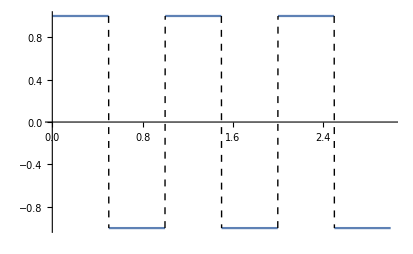

-Graphics-

```mathematica
Plot[{SquareWave[x],%},{x,0,3},ExclusionsStyle->Dashed]
Plot[{SquareWave[x]},{x,0,3},ExclusionsStyle->Dashed]
```

{1,-1,1,-1}

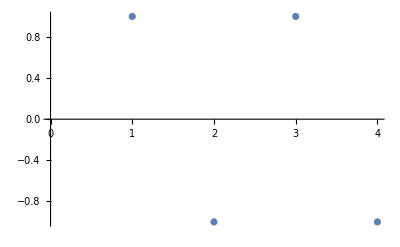

{1,-1,1,-1,1,-1,1}

```mathematica
t=Table[SquareWave[x/2],{x,0,3}]
ListPlot[t]
{1,-1,1,-1,1,-1,1}
```

```mathematica
FunctionPeriod[Sin[x*r*Pi],x]
```

0